```mathematica
Baxter=(α+β u^2)Q[u]+(u+I/2)^2 Q[u+I]+(u-I/2)^2 Q[u-I]
```

(α+u^2 β) Q[u]+(-ⅈ/2+u)^2 Q[-ⅈ+u]+(ⅈ/2+u)^2 Q[ⅈ+u]

```mathematica
1/u^S Baxter/.Q[u_]->u^S/.(u+a_)^S->u^S(1+a/u)^S
Series[1/u^S Baxter/.Q[u_]->u^S/.(u+a_)^S->u^S(1+a/u)^S,{u,∞,1}]
%==0
%//LogicalExpand
%//Solve//Last
slα=%;
```

u^-S ((1-ⅈ/u)^S u^S (-ⅈ/2+u)^2+(1+ⅈ/u)^S u^S (ⅈ/2+u)^2+u^S (α+u^2 β))

(2+β) u^2+(-1/2-S-S^2+α)+O[1/u]^2

(2+β) u^2+(-1/2-S-S^2+α)+O[1/u]^2==0

-1/2-S-S^2+α==0&&2+β==0

{α→1/2 (1+2 S+2 S^2),β→-2}

```mathematica
ℚ[S0_?EvenQ]:=Block[{P,ls},
P[u_]=Sum[a[n]u^n,{n,0,S0}]/.a[0]->1;
ls=Series[Baxter/.slα/.Q[u_]->P[u],{u,0,S0+2}]==0//LogicalExpand//Solve//Normal//Last;
P[u]/.ls]
ℚ[10]
```

1-(28878652 u^2)/893025+(1124492512 u^4)/11252115-(27474304 u^6)/382725+(8090368 u^8)/535815-(47297536 u^10)/56260575

```mathematica
tb=Table[{S,2+S+4I g^2 D[Log[ℚ[S]],u]/.u->I/2},{S,2,20,2}]
```

{{2,4+12 g^2},{4,6+(50 g^2)/3},{6,8+(98 g^2)/5},{8,10+(761 g^2)/35},{10,12+(7381 g^2)/315},{12,14+(86021 g^2)/3465},{14,16+(1171733 g^2)/45045},{16,18+(2436559 g^2)/90090},{18,20+(14274301 g^2)/510510},{20,22+(55835135 g^2)/1939938}}

```mathematica
ee=FindSequenceFunction[%,S]//FullSimplify
```

2+S+8 g^2 HarmonicNumber[S]

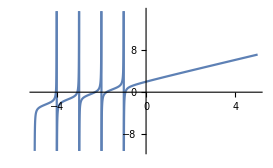

```mathematica
Plot[ee/.g->1/10,{S,-5,5}]
```

```mathematica
Series[ee,{S,∞,0}]//PowerExpand//Normal
```

2+8 EulerGamma g^2+S+8 g^2 Log[S]

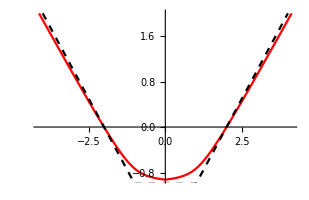

```mathematica
S0=S/.FindRoot[ee==0/.g->1/10,{S,-1+1/100}];
pp=ParametricPlot[{{ee/.g->1/10,S},{-ee/.g->1/10,S}},{S,S0,2},PlotStyle->Red];
pl=Plot[{{-2+x},{-2-x},{-1 If[Abs[x]<1,1,df]}},{x,-4,4},PlotStyle->{{Dashed,Black}}];
Show[pp,pl]
```

# Solving Baxter for any S

-Graphics-

```mathematica
𝕌=-I w D[#,w]&; 
Melin=Expand[(#/.u^(a_.)Q[u_]:>Nest[U,Q[u],a]/.Q[u+b_.]->w^(b/I) f[w])/.U->𝕌]&;
```

```mathematica
bax=(α+β u^2)Q[u]+(u+I/2)^2 Q[u+I]+(u-I/2)^2 Q[u-I]/.slα//Expand;
mbax=Collect[bax//Melin,{f[_],f'[_]},Simplify]
```

(S+S^2-(-1+w)^2/(4 w)) f[w]-2 (-1+w) w f'[w]-(-1+w)^2 w f''[w]

```mathematica
DSolve[mbax==0,f,w]
```

{{f→DifferentialRoot[Function[{y,x},{(1-2 x+x^2-4 x S-4 x S^2) y[x]+8 (-1+x) x^2 y'[x]+4 (-1+x)^2 x^2 y''[x]==0,y[2]==C[1],y'[2]==C[2]}],«»]}}

```mathematica
ee=Collect[mbax/.f:>(g[1/(1-#)]&)/.w->(z-1)/z//Simplify,g[__],Simplify]
```

((-1+4 S (-1+z) z+4 S^2 (-1+z) z) g[z])/(4 (-1+z) z)-(-1+z) z g''[z]

```mathematica
DSolve[ee==0,g[z],z]
```

{{g[z]→√(1-z) √z C[1] LegendreP[S,-1+2 z]+√(1-z) √z C[2] LegendreQ[S,-1+2 z]}}

```mathematica
rec=Collect[1/z^n Collect[ee/(√z √(1-z))/.g->(√#√(1-#)c[n]#^n &)//Simplify,z]/. a_ z^(n-1):>(a z^(n-1)/.n->n+1),c[n]]
```

(-n-n^2+S (1+S)) c[n]+(1+n)^2 c[1+n]

```mathematica
sol=c[n]/.RSolve[rec==0,c[n],n]//Last
```

(C[1] Pochhammer[1-S,-1+n] Pochhammer[2+S,-1+n])/Pochhammer[2,-1+n]^2

```mathematica
gz=Sum[% z^n √z √(1-z),{n,0,∞}]/.C[1]->1
```

-(√(1-z) √z Hypergeometric2F1[-S,1+S,1,z])/(S (1+S))

```mathematica
tn=gz Dt[w]/(Dt[z]w)w^(Zeta[3]+1/2)/.w->(z-1)/z//Simplify[#,z>0&&z<1]&//PowerExpand
```

(ⅈ (-1+z)^Zeta[3] z^(-1-Zeta[3]) Hypergeometric2F1[-S,1+S,1,z])/(S (1+S))

```mathematica
q[u_]=(S^2+S)/π Exp[π u]Cosh[π u]Integrate[tn,{z,0,1}]/.Zeta[3]->I u-1/2//FullSimplify
```

HypergeometricPFQ[{-S,1+S,1/2-ⅈ u},{1,1},1]

```mathematica
%/.S->12//Expand
ℚ[12]
%/%%//Simplify
```

53361/1048576-(12272016991 u^2)/6812467200+(2561060957 u^4)/398131200-(143126893 u^6)/24883200+(99058609 u^8)/58060800-(558467 u^10)/3110400+(96577 u^12)/17107200

1-(98176135928 u^2)/2773437975+(5853853616 u^4)/46309725-(747764992 u^6)/6615675+(25359003904 u^8)/756392175-(163391488 u^10)/46309725+(395579392 u^12)/3565848825

1048576/53361

# Extras

```mathematica
q[u_]=HypergeometricPFQ[{-S,S+1,1/2-ⅈ u},{1,1},1]/.S->200//Factor;
```

```mathematica
us=u/.Solve[q[u]==0//N[#,200]&,u]//Union;
```

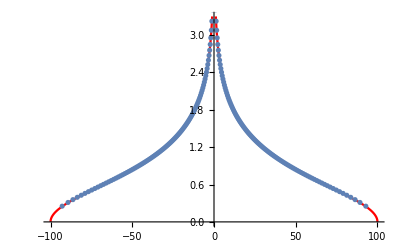

```mathematica
lp=ListPlot[Table[{(us[[i]]+us[[i+1]])/2,1/(us[[i+1]]-us[[i]])},{i,Length[us]-1}]];
pl=Plot[2/π ArcTanh[√(1-4u^2/200^2)],{u,-100,100},PlotStyle->Red];
Show[pl,lp]
```

```mathematica
eq=(S+1)/(-4 g^2)-PolyGamma[0,1/2-Δ/2]-PolyGamma[0,1/2+Δ/2]+2 PolyGamma[0,1]
```

-2 EulerGamma-(1+S)/(4 g^2)-PolyGamma[0,1/2-Δ/2]-PolyGamma[0,1/2+Δ/2]

```mathematica
Series[eq/.Δ->(Δ0=1+Sum[a[n](g^2/(S+1))^n,{n,1,20}]),{g,0,20}]==0//LogicalExpand;
res=Series[Δ0/.(Solve[%,Table[a[i],{i,20}]])//Last//FunctionExpand,{g,0,20}]
```

1-(8 g^2)/(1+S)-(1024 Zeta[3] g^8)/(1+S)^4-(16384 Zeta[5] g^12)/(1+S)^6-(393216 Zeta[3]^2 g^14)/(1+S)^7-(262144 Zeta[7] g^16)/(1+S)^8-(16777216 (Zeta[3] Zeta[5]) g^18)/(1+S)^9+(-(201326592 Zeta[3]^3)/(1+S)^10-(4194304 Zeta[9])/(1+S)^10) g^20+O[g]^21

```mathematica
Coefficient[res,g,20]g^20
```

g^20 (-(201326592 Zeta[3]^3)/(1+S)^10-(4194304 Zeta[9])/(1+S)^10)